```mathematica
λ1:= 1; 
λ2:=677*^8;
λ3:=203*^13; 
λ4:=182*^2; 
λ5:=593*^2; 
λ6:= 279*^4; 
λ7:=427*^9;
λ8:= 759*^12; 
λ9:=940*^14;
λ10:= 869*^11; 
λ11:=118*^12; 
λ12 := 862*^18;
λ13 := 181*^13;
λ14 := 201*^6;
λ15 := 326*^9;
λ16 :=118*^8;
λ17 :=283*^12;
λ18 := 559*^12;
b8b:=2*^-4;
b8a:=9998*^-4; 
b11b:= 9998*^-4;
b11a:= 2*^-4;
b14b :=1*^0; 
b14a:=19*^-9;b15b:=1*^0;b15a:=13*^-7;
```

```mathematica
m[l1_,l2_,l3_,l4_,l5_,l6_,l7_,l8_,l9_,l10_,l11_,l12_,l13_,l14_,l15_,l16_,l17_,l18_,b8a_,b8b_,b11a_,b11b_,b14a_,b14b_,b15a_,b15b_]:= -{{l1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-l1,l2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-l2,l3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,-l3,l4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,-l4, l5, 0,0,0,0,0,0,0,0,0,0,0,0,0,0}, {0,0,0,0,-l5, l6,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,-l6, l7,0,0,0,0,0,0,0,0,0,0,0,0},{0, 0, 0, 0, 0, 0, -l7, l8,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,-l8*b8b, l9, 0, 0, 0, 0, 0, 0, 0,0,0,0}, {0,0,0,0,0,0,0,-l8*b8a,0, l10,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,-l9,-l10,l11,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,-l11*b11b,l12,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,-l11*b11a,0,l13,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,-l12,-l13,l14,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,-l14*b14b,l15,0,0,0,0} ,{0,0,0,0,0,0,0,0,0,0,0,0,0,0,-l15*b15b,l16,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,-l14*b14a,0,0,l17,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,-l15*b15a,0,-l17,l18,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-l16,0,-l18,0}}
```

```mathematica
f := {n1[t],n2[t],n3[t],n4[t],n5[t],n6[t],n7[t],n8[t],n9[t],n10[t],n11[t],n12[t],n13[t],n14[t],n15[t],n16[t],n17[t],n18[t],n19[t]}
```

```mathematica
LHS = m[λ1,λ2,λ3,λ4,λ5,λ6,λ7,λ8,λ9,λ10,λ11,λ12,λ13,λ14,λ15,λ16,λ17,λ18,b8a,b8b,b11a,b11b,b14a,b14b,b15a,b15b].f
```

{-n1[t],n1[t]-67700000000 n2[t],67700000000 n2[t]-2030000000000000 n3[t],2030000000000000 n3[t]-18200 n4[t],18200 n4[t]-59300 n5[t],59300 n5[t]-2790000 n6[t],2790000 n6[t]-427000000000 n7[t],427000000000 n7[t]-759000000000000 n8[t],151800000000 n8[t]-94000000000000000 n9[t],-86900000000000 n10[t]+758848200000000 n8[t],86900000000000 n10[t]-118000000000000 n11[t]+94000000000000000 n9[t],117976400000000 n11[t]-862000000000000000000 n12[t],23600000000 n11[t]-1810000000000000 n13[t],862000000000000000000 n12[t]+1810000000000000 n13[t]-201000000 n14[t],201000000 n14[t]-326000000000 n15[t],326000000000 n15[t]-11800000000 n16[t],(3819 n14[t])/1000-283000000000000 n17[t],423800 n15[t]+283000000000000 n17[t]-559000000000000 n18[t],11800000000 n16[t]+559000000000000 n18[t]}

```mathematica
Eqns1 = LHS[[1]]==n1'[t]
```

-n1[t]==n1'[t]

```mathematica
Eqns2 = LHS[[2]]==n2'[t]
```

n1[t]-67700000000 n2[t]==n2'[t]

```mathematica
Eqns3 = LHS[[3]]==n3'[t]
```

67700000000 n2[t]-2030000000000000 n3[t]==n3'[t]

```mathematica
Eqns4 = LHS[[4]]==n4'[t]
```

2030000000000000 n3[t]-18200 n4[t]==n4'[t]

```mathematica
Eqns5 = LHS[[5]]==n5'[t]
```

18200 n4[t]-59300 n5[t]==n5'[t]

```mathematica
Eqns6 = LHS[[6]]==n6'[t]
```

59300 n5[t]-2790000 n6[t]==n6'[t]

```mathematica
Eqns7 = LHS[[7]]==n7'[t]
```

2790000 n6[t]-427000000000 n7[t]==n7'[t]

```mathematica
Eqns8 = LHS[[8]]==n8'[t]
```

427000000000 n7[t]-759000000000000 n8[t]==n8'[t]

```mathematica
Eqns9 = LHS[[9]]==n9'[t]
```

151800000000 n8[t]-94000000000000000 n9[t]==n9'[t]

```mathematica
Eqns10 = LHS[[10]]==n10'[t]
```

-86900000000000 n10[t]+758848200000000 n8[t]==n10'[t]

```mathematica
Eqns11 = LHS[[11]]==n11'[t]
```

86900000000000 n10[t]-118000000000000 n11[t]+94000000000000000 n9[t]==n11'[t]

```mathematica
Eqns12 = LHS[[12]]==n12'[t]
```

117976400000000 n11[t]-862000000000000000000 n12[t]==n12'[t]

```mathematica
Eqns13 = LHS[[13]]==n13'[t]
```

23600000000 n11[t]-1810000000000000 n13[t]==n13'[t]

```mathematica
Eqns14 = LHS[[14]]==n14'[t]
```

862000000000000000000 n12[t]+1810000000000000 n13[t]-201000000 n14[t]==n14'[t]

```mathematica
Eqns15 = LHS[[15]]==n15'[t]
```

201000000 n14[t]-326000000000 n15[t]==n15'[t]

```mathematica
Eqns16 = LHS[[16]]==n16'[t]
```

326000000000 n15[t]-11800000000 n16[t]==n16'[t]

```mathematica
Eqns17 = LHS[[17]]==n17'[t]
```

(3819 n14[t])/1000-283000000000000 n17[t]==n17'[t]

```mathematica
Eqns18 = LHS[[18]]==n18'[t]
```

423800 n15[t]+283000000000000 n17[t]-559000000000000 n18[t]==n18'[t]

```mathematica
Eqns19 = LHS[[19]]==n19'[t]
```

11800000000 n16[t]+559000000000000 n18[t]==n19'[t]

```mathematica
sol=NDSolve[{Eqns1,Eqns2,Eqns3,Eqns4,Eqns5,Eqns6,Eqns7,Eqns8,Eqns9,Eqns10,Eqns11,Eqns12,Eqns13,Eqns14,Eqns15,Eqns16,Eqns17,Eqns18,Eqns19,n1[0]==1,n2[0]==0,n3[0]==0,n4[0]==0,n5[0]==0,n6[0]==0,n7[0]==0,n8[0]==0,n9[0]==0,n10[0]==0,n11[0]==0,n12[0]==0,n13[0]==0,n14[0]==0,n15[0]==0,n16[0]==0,n17[0]==0,n18[0]==0,n19[0]==0},{n1,n2,n3,n4,n5,n6,n7,n8,n9,n10,n11,n12,n13,n14,n15,n16,n17,n18,n19},{t,0,1}];
```

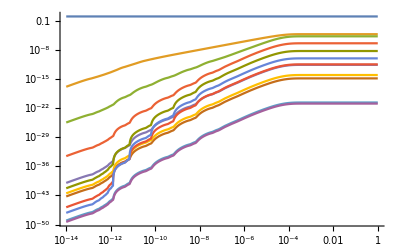

```mathematica
LogLogPlot[Evaluate[{n1[t]/n1[t],n4[t]/n1[t],n5[t]/n1[t],n6[t]/n1[t],n7[t]/n1[t],n8[t]/n1[t],n9[t]/n1[t],n11[t]/n1[t],n12[t]/n1[t],n14[t]/n1[t],n15[t]/n1[t],n16[t]/n1[t]}/. sol],{t,1*^-14,1},PlotRange->All]
```

```mathematica
Evaluate[9*^-15*{n1[1]/n1[1],n4[1]/n1[1],n5[1]/n1[1],n6[1]/n1[1],n7[1]/n1[1],n8[1]/n1[1],n9[1]/n1[1],n11[1]/n1[1],n12[1]/n1[1],n14[1]/n1[1],n15[1]/n1[1],n16[1]/n1[1]}/. sol]
```

{{9/1000000000000000,4.94533×10^-19,1.51782×10^-19,3.22604×10^-21,2.10788×10^-26,1.18586×10^-29,1.91503×10^-35,7.62767×10^-29,1.04395×10^-35,4.47794×10^-23,2.76094×10^-26,7.62767×10^-25}}